```mathematica
(*Import all simulations*)
(*Average all simulations*)
(*Extract mean, median & mode*)
(*Plot averages*)
```

```mathematica
(*Single Simulations*)
```

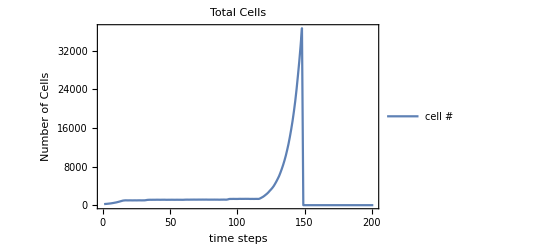

```mathematica
data=Import["/Users/arturo/Desktop/AneyploidySim0.1/CellGrowth/data mutation low Long/C 7 of 10000.txt",{"Data",{All}}];
ListLinePlot[{data[[All,24]]}, PlotLegends->{"cell #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Total Cells",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

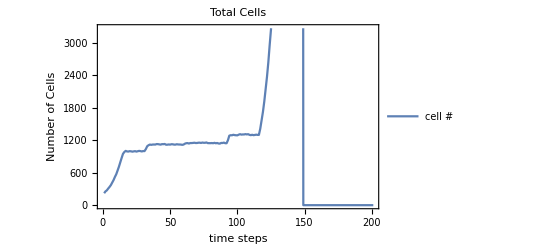

```mathematica
ListLinePlot[{data[[All,24]]}, PlotLegends->{"cell #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Total Cells",PlotRange-> Automatic, AspectRatio->1/GoldenRatio]
```

```mathematica
(*All Simualtions that resulted in Cancer*)
```

```mathematica
files=FileNames["C*",{"/Users/arturo/Desktop/AneyploidySim0.1/CellGrowth/data mutation low Long/"}];
dataAll=Table[Import[files[[j]],"Data"],{j,1,Length[files]}];
Length[dataAll]
```

442

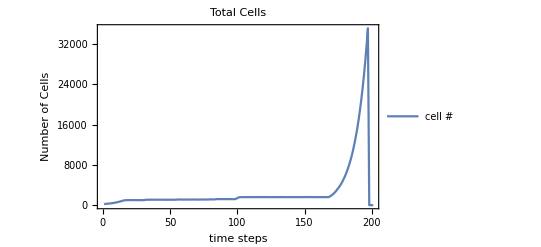

```mathematica
data2=dataAll[[3]];
ListLinePlot[{data2[[All,24]]}, PlotLegends->{"cell #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Total Cells",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

```mathematica
ListLinePlot[{dataAll[[3]][[All,24]]}, PlotLegends->{"cell #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Total Cells",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*Average all Simulations*)
```

```mathematica
dataAllMean=Mean[dataAll];
```

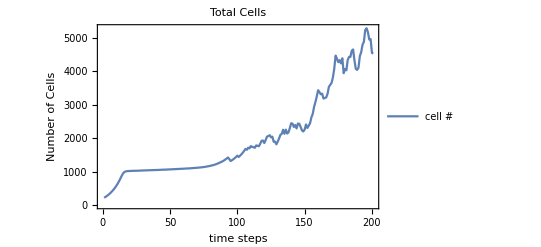

```mathematica
fig3=ListLinePlot[{dataAllMean[[All,24]]}, PlotLegends->{"cell #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Total Cells",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

```mathematica
Export["/Users/arturo/Dropbox/ALife 2020/PIxelmator/results/data mutation low Long 1.pdf",fig3];
```

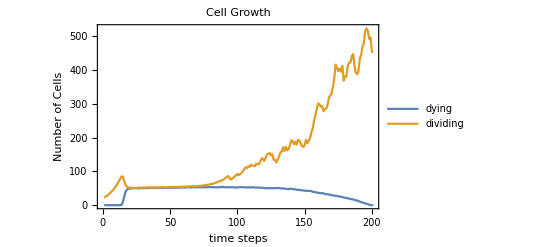

```mathematica
fig4=ListLinePlot[{dataAllMean[[All,4]],dataAllMean[[All,5]]}, PlotLegends->{"dying","dividing"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Cell Growth",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

```mathematica
Export["/Users/arturo/Dropbox/ALife 2020/PIxelmator/results/data mutation low Long 2.pdf",fig4];
```

```mathematica
(*gene copy #*)
```

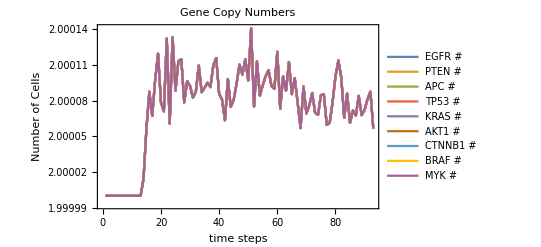

```mathematica
fig5=ListLinePlot[{
dataAllMean[[All,6]],
dataAllMean[[All,7]],
dataAllMean[[All,8]],
dataAllMean[[All,9]],
dataAllMean[[All,10]],
dataAllMean[[All,11]],
dataAllMean[[All,12]],
dataAllMean[[All,13]],
dataAllMean[[All,14]]}, PlotLegends->{"EGFR #","PTEN #","APC #","TP53 #","KRAS #","AKT1 #","CTNNB1 #","BRAF # ","MYK #"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Gene Copy Numbers",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

```mathematica
Export["/Users/arturo/Dropbox/ALife 2020/PIxelmator/results/data mutation low Long 3.pdf",fig5];
```

```mathematica
(*gene mutations*)
```

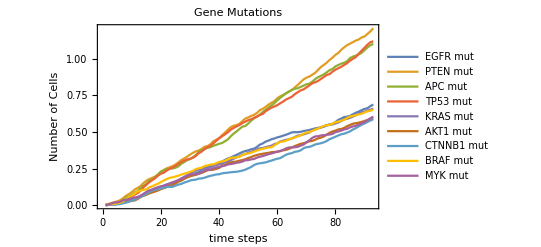

```mathematica
fig6= ListLinePlot[{
dataAllMean[[All,15]],
dataAllMean[[All,16]],
dataAllMean[[All,17]],
dataAllMean[[All,18]],
dataAllMean[[All,19]],
dataAllMean[[All,20]],
dataAllMean[[All,21]],
dataAllMean[[All,22]],
dataAllMean[[All,23]]}, PlotLegends->{"EGFR mut","PTEN mut","APC mut","TP53 mut","KRAS mut","AKT1 mut","CTNNB1 mut","BRAF mut ","MYK mut"}, Frame->True, FrameLabel-> {"time steps", "Number of Cells"},PlotLabel-> "Gene Mutations",PlotRange-> All, AspectRatio->1/GoldenRatio]
```

```mathematica
Export["/Users/arturo/Dropbox/ALife 2020/PIxelmator/results/data mutation low Long 4.pdf",fig6];
```